```mathematica
DATA1={2.6,2.7,3.4,3.6,3.7,3.9,4.0,4.4,4.8,4.8,4.8,5.0,5.1,5.6,
5.6,5.6,5.8,6.8,7.0,7.0};
```

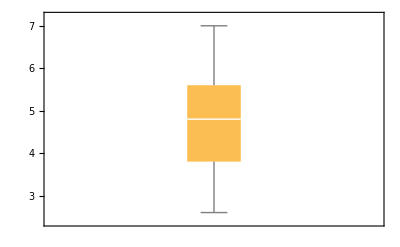

```mathematica
BoxWhiskerChart[DATA1]
```

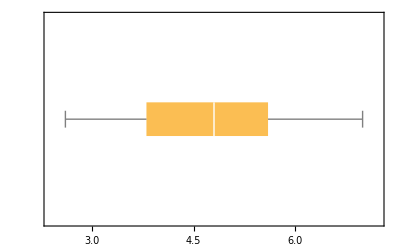

```mathematica
BoxWhiskerChart[DATA1,BarOrigin->Left]
```

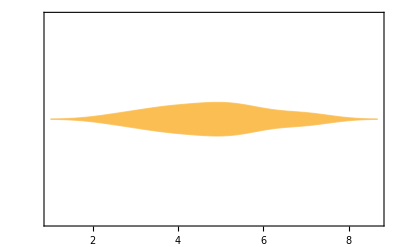

```mathematica
DistributionChart[DATA1,BarOrigin->Left]
```

```mathematica
DATA2={2.6,2.7,3.4,3.6,3.7,3.9,4.0,4.4,4.8,4.8,
4.8,5.0,5.1,5.6,5.6,5.6,5.8,6.8,7.0,7.0,13.0};
```

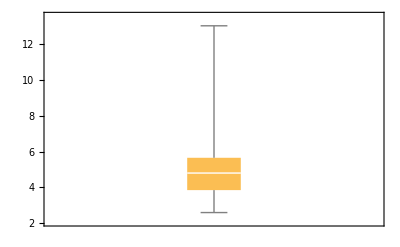

```mathematica
BoxWhiskerChart[DATA2]
```

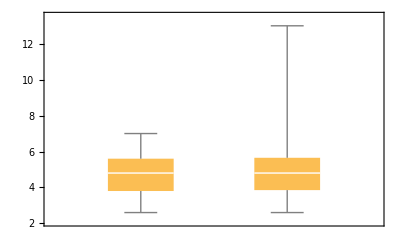

```mathematica
BoxWhiskerChart[{DATA1,DATA2}]
```

```mathematica
LocationStatistics[data_]:=<|"Mean"->Mean[data],"Median"->Median[data],"Mode"->
Commonest[data],"TrimmedMean"->TrimmedMean[data],"WinsoredMean"->WinsorizedMean[data],
"BiweightLocation"->BiweightLocation[data],"CentralFeature"->CentralFeature[data],
"HarmonicMean"->HarmonicMean[data],"GeometricMean"->GeometricMean[data]
"ContraharmonicMean"->ContraharmonicMean[data]|>
```

```mathematica
LocationStatistics[DATA1]
```

<|Mean→4.81,Median→4.8,Mode→{4.8,5.6},TrimmedMean→4.81111,WinsoredMean→4.815,BiweightLocation→4.79091,CentralFeature→4.8,HarmonicMean→4.45155,GeometricMean→4.63439 ContraharmonicMean→5.1447|>

```mathematica
3.8-1.5(5.6-3.8)
```

1.1

```mathematica
5.6+1.5(5.6-3.8)
```

8.3

```mathematica
3.85-(5.65-3.85)1.5
```

1.15

```mathematica
5.65+(5.65-3.85)1.5
```

8.35

```mathematica
?CentralFeature
```